Program Overview:
This program accepts frequency values input by the user,which then serves as the basis for acoustic simulation,yielding a perfectly matched simulation result.Simultaneously,the program provides corresponding parameter values for capacitance,inductance,and resistance,offering concrete references for acoustic design.Program Functions
Frequency Value Input:
Users can input specific frequency values,which form the foundation for acoustic simulations.Frequency describes the speed of sound wave vibrations,with different frequencies leading to varying acoustic effects.By inputting specific frequency values,users can simulate specific acoustic effects.Perfectly Matched Simulation Results
Based on the user-input frequency values,the program performs acoustic simulations,generating perfectly matched simulation results.These results represent the propagation and reaction of sound waves at the given frequency in real-world situations.Parameter Value Output
In addition to simulation results,the program also provides corresponding parameter values for capacitance,inductance,and resistance.These three factors significantly influence sound wave propagation.By adjusting these parameter values,one can optimize acoustic effects.The parameter values provided by the program serve as references for acoustic design.

-Graphics-

-Graphics-

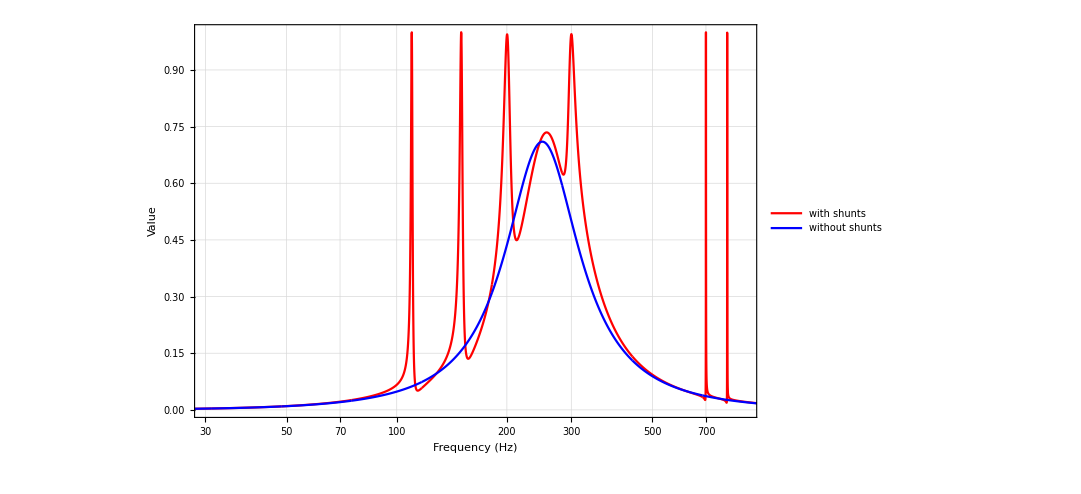

Parameters | Values |  |  |  |  | 
fe\hz | 110 | 150 | 200 | 300 | 700 | 800
Lp\H | 1/10 | 1/10 | 1/10 | 1/10 | 1/10 | 1/10
Rp\ohm | 0.198211 | 0.736176 | 3.37866 | 4.41746 | 0.0698609 | 0.0221106
Cp\F | 0.0000203765 | 0.000010904 | 6.07588×10^-6 | 2.89331×10^-6 | 5.17766×10^-7 | 3.96101×10^-7

```mathematica
(*声明变量*)BL2=4.6^2;
freq=10^Range[Log10[20],Log10[5000],(Log10[5000]-Log10[20])/99999];
c0=343;
Wd=0.08;
rcA=1.25*c0*Wd^2;
dep=0.15;
k0=1000;
w=2*Pi*freq;
s=I*w;
k=w/c0;
mass=4*10^-3;
stiff=(2*Pi*250)^2*mass;
d=rcA*0.3;
Rc=0.1;
Lc=0.15*10^-3;
Noct=Sqrt[2];
(*getNfe[]:=Module[{nfe=-1},While[nfe<=0,nfe=Input["Please enter the number of frequencies that need to be perfectly matched:"];
If[!IntegerQ[nfe]||nfe<=0,Print["Invalid input. Nfe must be a positive integer."];];];
nfe]

getNfe[]:=Module[{nfe=-1},While[nfe<=0,nfe=Input["Enter a positive integer for Nfe"];
If[!IntegerQ[nfe]||nfe<=0,Print["Invalid input. Nfe must be a positive integer."];];];
nfe]

getFe[nfe_]:=Module[{fe={}},While[Length[fe]!=nfe,fe=Input["Enter a list of length "<>ToString[nfe]<>" for fe"];
If[!ListQ[fe]||Length[fe]!=nfe||!AllTrue[fe,NumericQ],Print["Invalid input. fe must be a list of length "<>ToString[nfe]<>" with numeric elements."];
fe={};];];
fe]*)
getFe[]:=Module[{fe={}},While[!ListQ[fe]||Length[fe]==0||!AllTrue[fe,NumericQ],fe=Input["Please enter an array of frequencies to be perfectly matched, enclosed in curly braces. The format should be {f1, f2, f3, f4}:
"];
If[!ListQ[fe]||Length[fe]==0||!AllTrue[fe,NumericQ],Print["Invalid input. fe must be a non-empty numeric list."];
fe={};];];
fe]

fe=getFe[];
Nfe=Length[fe];
Lp=Table[100*10^-3,{i,0,Nfe-1}];



pdAfaComb[L_,fr_,m_,dep_,k0_,d_,BL2_,rcA_]:=Module[{wr,s,k,Xm,Xe,c,R},wr=fr*2*Pi;
s=I*wr;
k=k0;
Xm=Im[m*s+k/s];
Xe=BL2*Xm/(Xm^2+(rcA-d)^2);
c=1/(wr*L-Xe)/wr;
R=BL2*(rcA-d)/(Xm^2+(rcA-d)^2);
{R,c}]


RCL=pdAfaComb[Lp+Lc,fe,mass,dep,stiff,d,BL2,rcA];
Rp=First[RCL]-Rc;
If[Min[Rp]<0,Print["Rp=",Min[Rp],"ohm <0"];Return[]];

Ap=Table[1/(Rp[[n]]+Lp[[n]]*s+1/(Last[RCL][[n]]*s)),{n,1,Nfe}];
Zc=Rc+Lc*s;
Zp=1/Total[Ap];
Ze=Zc+Zp;
Zm=(mass*s+d+stiff/s)/rcA;
dZ=BL2/Ze/rcA;
Z=Zm+dZ;
beta=Abs[(1-Z)/(1+Z)]^2;
betam=Abs[(1-Zm)/(1+Zm)]^2;
alfa=1-beta;
alfam=1-betam;
ZValues=Z/. s->freq;
ZmValues=Zm/. s->freq;
alfaValues=alfa/. s->freq;
alfamValues=alfam/. s->freq;


ZRealValues=Re[ZValues];
ZmRealValues=Re[ZmValues];
ZImagValues=Im[ZValues];
ZmImagValues=Im[ZmValues];
(*第一张图：Z和Zm的实值*)ListLogLogPlot[{Transpose[{freq,ZRealValues}],Transpose[{freq,ZmRealValues}]},PlotRange->{{30,900},{0.2,60}},PlotLegends->{"with shunts","without shunts"},AxesLabel->{"Frequency (Hz)","Real Value"},Joined->True,PlotTheme->"Detailed",PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick]},LabelStyle->{FontSize->14,FontFamily->"Helvetica"},GridLines->Automatic,ImageSize->{800,300}]

(*放大镜图*)
zoomedPlot=ListLogLinearPlot[{Transpose[{freq,ZImagValues}],Transpose[{freq,ZmImagValues}]},PlotRange->{{200,370},{-36,25}},PlotLegends->{"with shunts","without shunts"},AxesLabel->{"Frequency (Hz)","Imaginary Value"},Joined->True,ImageSize->300,PlotTheme->"Detailed",PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick]},LabelStyle->{FontSize->14,FontFamily->"Helvetica"},GridLines->Automatic,ImageSize->{200,100}];

(*第二张图：Z和Zm的虚值*)
ListLogLinearPlot[{Transpose[{freq,ZImagValues}],Transpose[{freq,ZmImagValues}]},PlotRange->{{30,900},{-36,25}},PlotLegends->{"with shunts","without shunts"},AxesLabel->{"Frequency (Hz)","Imaginary Value"},Joined->True,Epilog->Inset[zoomedPlot,{100,0},{Left,Bottom}],PlotTheme->"Detailed",PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick]},LabelStyle->{FontSize->14,FontFamily->"Helvetica"},GridLines->Automatic,ImageSize->{800,300}]

(*第三张图：alfa和alfam的值*)
ListLogLinearPlot[{Transpose[{freq,alfaValues}],Transpose[{freq,alfamValues}]},PlotRange->{{30,900},All},PlotLegends->{"with shunts","without shunts"},AxesLabel->{"Frequency (Hz)","Value"},Joined->True,PlotTheme->"Detailed",PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick]},LabelStyle->{FontSize->14,FontFamily->"Helvetica"},GridLines->Automatic,ImageSize->{800,300}]
(*打印fe、Lp、Rp和C的列表*)Print[TableForm[{Prepend[fe,"fe\hz"],Prepend[Lp,"Lp\H"],Prepend[Rp,"Rp\ohm"],Prepend[Last[RCL],"Cp\F"]},TableAlignments->Left,TableHeadings->{None,{"Parameters","Values"}}]]
(*(*第一张图：Z和Zm的实值*)
ListLogLogPlot[{Transpose[{freq,ZRealValues}],Transpose[{freq,ZmRealValues}]},PlotRange->{{30,800},{0.2,60}},PlotLegends->{"with shunts","without shunts"},AxesLabel->{"Frequency (Hz)","Real Value"},Joined->True]

zoomedPlot=ListLogLinearPlot[{Transpose[{freq,ZImagValues}],Transpose[{freq,ZmImagValues}]},PlotRange->{{180,220},{-36,25}},PlotLegends->{"with shunts","without shunts"},AxesLabel->{"Frequency (Hz)","Imaginary Value"},Joined->True,ImageSize->300]


ListLogLinearPlot[{Transpose[{freq,ZImagValues}],Transpose[{freq,ZmImagValues}]},PlotRange->{{30,800},{-36,25}},PlotLegends->{"with shunts","without shunts"},AxesLabel->{"Frequency (Hz)","Imaginary Value"},Joined->True,Epilog->Inset[zoomedPlot,{600,0},{Left,Bottom}]]
(*第三张图：alfa和alfam的值*)
ListLogLinearPlot[{Transpose[{freq,alfaValues}],Transpose[{freq,alfamValues}]},PlotRange->{{30,800},All},PlotLegends->{"alfa with shunts","alfa without shunts"},AxesLabel->{"Frequency (Hz)","alfa"},Joined->True]
(*打印fe、Lp、Rp和C的列表*)Print[TableForm[{Prepend[fe,"fe\hz"],Prepend[Lp,"Lp\H"],Prepend[Rp,"Rp\ohm"],Prepend[Last[RCL],"Cp\F"]},TableAlignments->Left,TableHeadings->{None,{"Parameters","Values"}}]]*)
```

inductance, capacitance, and resistance

The demonstration illustrates how the desired absorption frequency impacts the circuit’s necessary frequency, inductance, capacitance, and resistance. As the desired absorption frequency alters, these parameters experience a relative variation to maintain the optimal acoustic performance.

```mathematica
Manipulate[Module[{BL2=4.6^2,c0=343,Wd=0.08,rcA=1.25*c0*Wd^2,dep=0.15,k0=1000,mass=4*10^-3,stiff=(2*Pi*250)^2*mass,d=rcA*0.3,Rc=0.1,Lc=0.15*10^-3,pdAfaComb,Lp,feRange={100,3000},rpFunc,cpFunc},pdAfaComb[L_,fr_,m_,dep_,k0_,d_,BL2_,rcA_]:=Module[{wr,s,k,Xm,Xe,c,R},wr=fr*2*Pi;
s=I*wr;
k=k0;
Xm=Im[m*s+k/s];
Xe=BL2*Xm/(Xm^2+(rcA-d)^2);
c=1/(wr*L-Xe)/wr;
R=BL2*(rcA-d)/(Xm^2+(rcA-d)^2);
{R,c}];
Lp=l;
rpFunc[fe_]:=First[pdAfaComb[Lp+Lc,fe,mass,dep,stiff,d,BL2,rcA]]-Rc;
cpFunc[fe_]:=Last[pdAfaComb[Lp+Lc,fe,mass,dep,stiff,d,BL2,rcA]];
(*创建两个单独的图表*)Grid[{{Plot[rpFunc[fe],{fe,feRange[[1]],feRange[[2]]},AxesLabel->{"Frequency (Hz)","Rp"},PlotRange->All,PlotLabel->"Rp vs fe",ImageSize->Large]},{Plot[cpFunc[fe],{fe,feRange[[1]],feRange[[2]]},AxesLabel->{"Frequency (Hz)","Cp"},PlotRange->All,PlotLabel->"Cp vs fe",ImageSize->Large]}}]],{l,0.01,0.1,0.001}]
```